### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

```mathematica
cols=ColorData[97,"ColorList"]⟦{2,1,3}⟧
```

{RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885]}

## Data processing

### Type 1 Conformists

```mathematica
SetDirectory[NotebookDirectory[]<>"typeI_anticonformist_b-2/"]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/New_Revised_Figures/Fig_SI_anticonf/typeI_anticonformist_b-2

```mathematica
filenames=FileNames[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/New_Revised_Figures/Fig_SI_anticonf

```mathematica
filecounter=Range[0.0,1.0,0.05]/.{0.->"0.0",1.->"1.0"}
```

{0.0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.0}

```mathematica
filenames//Sort
```

{out_c0.05.csv,out_c0.0.csv,out_c0.15.csv,out_c0.1.csv,out_c0.25.csv,out_c0.2.csv,out_c0.35.csv,out_c0.3.csv,out_c0.45.csv,out_c0.4.csv,out_c0.55.csv,out_c0.5.csv,out_c0.65.csv,out_c0.6.csv,out_c0.75.csv,out_c0.7.csv,out_c0.85.csv,out_c0.8.csv,out_c0.95.csv,out_c0.9.csv,out_c1.0.csv,params.csv}

```mathematica
rawtype1anticonf={};
rawtype1anticonf=Table[Import[NotebookDirectory[]<>"typeII_anticonformist_f1.2/"<>"out_c"<>ToString[filecounter⟦i⟧]<>".csv","CSV"],{i,1,Length[filecounter],1}];
```

```mathematica
rawtype1anticonf//Dimensions
```

{21,1275,4}

### Type 2 Conformists

```mathematica
SetDirectory[NotebookDirectory[]<>"typeII_conformist_f1.2/"]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/New_Revised_Figures/Fig_3_overlays/typeII_conformist_f1.2

```mathematica
NotebookDirectory[]
```

/Users/chaitanyagokhale/Documents/Working/Srishti/Overleafdata/matecopying_multiplemorphs/New_Revised_Figures/Fig_3_overlays/

```mathematica
filenames=FileNames[];
```

```mathematica
filecounter=Range[0.0,1.0,0.05]/.{0.->"0.0",1.->"1.0"}
```

{0.0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.0}

```mathematica
filenames//Sort
```

{out_c0.05.csv,out_c0.0.csv,out_c0.15.csv,out_c0.1.csv,out_c0.25.csv,out_c0.2.csv,out_c0.35.csv,out_c0.3.csv,out_c0.45.csv,out_c0.4.csv,out_c0.55.csv,out_c0.5.csv,out_c0.65.csv,out_c0.6.csv,out_c0.75.csv,out_c0.7.csv,out_c0.85.csv,out_c0.8.csv,out_c0.95.csv,out_c0.9.csv,out_c1.0.csv,params.csv}

```mathematica
rawtype2conf={};
rawtype2conf=Table[Import[NotebookDirectory[]<>"typeII_conformist_f1.2/"<>"out_c"<>ToString[filecounter⟦i⟧]<>".csv","CSV"],{i,1,Length[filecounter],1}];
```

```mathematica
rawtype2conf//Dimensions
```

{21,1275,4}

## Analytics

### Type 1 Conformists

```mathematica
α=0.8;β=-2;γ=.;u=0;
q1=2;q2=2.5;q3=3;
p[γ_,y_,q_]:=(1-γ)q/(q1+q2+q3)+α γ (y^β/(y^β+(1-y)^β));
```

```mathematica
gammas=ReplacePart[Table[i,{i,0,1,0.05}],21->0.99]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,0.99}

```mathematica
internal={};
notransinternal={};
Table[
dy1[y1_,y2_]:=y1(p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2)));
dy2[y1_,y2_]:=y2 (p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2)));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<1.&&Total[#]>0&];
AppendTo[internal,{γ,If[relData=={},Missing[],trans[relData⟦1⟧]]}];
AppendTo[notransinternal,{γ,If[relData=={},Missing[],relData⟦1⟧]}];,{γ,gammas}
];
```

Part::partd: Part specification y1⟦1⟧ is longer than depth of object.

Part::partd: Part specification y1⟦2⟧ is longer than depth of object.

Part::partd: Part specification y2⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
internal={};
```

```mathematica
data
```

{{-2.02265,-9.26783},{0.404884,-10.5014},{-10.9556,7.96679},{-8.66169,9.09387},{-4.68564,0.512553}}

```mathematica
AppendTo[internal,{γ,If[data=={},Missing[],trans[data⟦1⟧]]}]
```

{{1.2,{4.12259,10.6439}}}

```mathematica
tlp=TernaryListPlot[{0.3,0.3,0.3},(*AxesStyle->cols⟦{1,3,2}⟧, Axes->True,*)FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,FrameStyle->Thickness[0.005]]
```

-Graphics-

```mathematica
internal
```

{{0.,Missing[]},{0.05,Missing[]},{0.1,Missing[]},{0.15,Missing[]},{0.2,Missing[]},{0.25,Missing[]},{0.3,Missing[]},{0.35,Missing[]},{0.4,Missing[]},{0.45,Missing[]},{0.5,{0.298383,0.481861}},{0.55,{0.324081,0.460465}},{0.6,{0.344025,0.443692}},{0.65,{0.35993,0.430096}},{0.7,{0.372891,0.418803}},{0.75,{0.383645,0.40924}},{0.8,{0.392703,0.401019}},{0.85,{0.400433,0.393861}},{0.9,{0.407102,0.387565}},{0.95,{0.412914,0.381976}},{0.99,Missing[]}}

```mathematica
inteqdyn=Show[tlp,ListPlot[internal⟦All,2⟧,Joined->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.005]],Mesh->All,MeshStyle->Directive[PointSize[Medium],Black]],
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]]
```

-Graphics-

### Type 2 conformists

#### Code for generating the copying probabilities

```mathematica
(* Parameters *)
factor = 1.2;  (* in the main text f = 1/factor = 1/1.2 *)
b = β;        (* for anticonformist, b = 2 for conformist *)

(* --------------------------------------------------------------------- *)
(* Compute D function *)
computeD[greaterVals_, b_, factor_] := Module[{ymax, Dmax, Dmin},
  Which[
    b >= 1,
    ymax = Max[greaterVals];
    Dmax = (1/ymax - 1) Total[greaterVals];
    Dmax/factor,
    
    b < 1,
    Dmin = -Total[greaterVals];
    Dmin/factor
  ]
]

(* --------------------------------------------------------------------- *)
(* Main function: switching probabilities *)
switchingProbabilities[y_List, b_, copyingType_: 1] := 
 Module[{probs, majority, greaterIdx, equalIdx, lessIdx,
   greaterVals, equalVals, lessVals, D, invY, factors,
   Dconf, Danti, threshold, maskConf, maskAnti, probSum},
  
  Which[
   (* --- Type I copying --- *)
   copyingType == 1,
   probs = (y^b)/(y^b + (1 - y)^b),
   
   (* --- Type II copying --- *)
   copyingType == 2,
   If[b == 1,
    probs = y, (* frequency proportional copying *)
    majority = 1/Length[y];
    greaterIdx = Flatten@Position[y, _?(# > majority &)];
    equalIdx = Flatten@Position[y, _?(# == majority &)];
    lessIdx = Flatten@Position[y, _?(# < majority &)];
    
    greaterVals = y[[greaterIdx]];
    equalVals = y[[equalIdx]];
    lessVals = y[[lessIdx]];
    
    If[Length[greaterVals] == 0, D = 0,
     D = computeD[greaterVals, b, factor]
    ];
    
    (* Adjust values *)
    If[Length[greaterVals] > 0,
     greaterVals = 
      greaterVals + (greaterVals/Total[greaterVals])*D;
    ];
    
    If[Length[lessVals] > 0,
     invY = 1/lessVals;
     factors = invY/Total[invY];
     lessVals = lessVals - factors*D;
    ];
    
    (* Construct probability vector *)
    probs = ConstantArray[0., Length[y]];
    probs[[greaterIdx]] = greaterVals;
    probs[[equalIdx]] = equalVals;
    probs[[lessIdx]] = lessVals;
    ],
   
   (* --- Type III copying (mixed) --- *)
   copyingType == 3,
   majority = 1/Length[y];
   greaterIdx = Flatten@Position[y, _?(# > majority &)];
   equalIdx = Flatten@Position[y, _?(# == majority &)];
   lessIdx = Flatten@Position[y, _?(# < majority &)];
   
   greaterVals = y[[greaterIdx]];
   equalVals = y[[equalIdx]];
   lessVals = y[[lessIdx]];
   
   If[Length[greaterVals] == 0,
    Dconf = 0; Danti = 0,
    Dconf = computeD[greaterVals, 2, factor];
    Danti = computeD[greaterVals, -2, factor];
   ];
   
   threshold = If[Length[y] == 2, 0.7, 0.5];
   
   If[Length[greaterVals] != 0,
    maskConf = Map[# < threshold &, greaterVals];
    maskAnti = Map[# >= threshold &, greaterVals];
    
    (* greater than majority (adjust according to threshold) *)
    greaterVals = 
     MapThread[
      If[#1, #2 + (#2/Total[greaterVals])*Dconf, 
        #2 + (#2/Total[greaterVals])*Danti] &, 
      {maskConf, greaterVals}
     ];
    
    (* less than majority *)
    invY = Table[If[Abs[val] > 10^-5, 1/val, 0], {val, lessVals}];
    If[Total[invY] == 0,
     factors = ConstantArray[0., Length[invY]],
     factors = invY/Total[invY]
    ];
    lessVals = lessVals - factors*Dconf;
   ];
   
   (* Construct probability vector *)
   probs = ConstantArray[0., Length[y]];
   probs[[greaterIdx]] = greaterVals;
   probs[[equalIdx]] = equalVals;
   probs[[lessIdx]] = lessVals;
   
   probs = Map[If[# > 10^-5, #, 0] &, probs];
   
   (* Normalize *)
   probSum = Total[probs];
   probs = probs/probSum;
   ];
  
  probs
]
```

```mathematica
f=1.2;
vectorofcopyingvalues[y_]:=switchingProbabilities[{y⟦1⟧, y⟦2⟧, 1-y⟦1⟧-y⟦2⟧}, b, 2];
typ2p[γ_,y_,q_,type_]:=(1-γ)q/(q1+q2+q3)+γ α Switch[type,1,vectorofcopyingvalues[y]⟦1⟧,2,vectorofcopyingvalues[y]⟦2⟧,3,vectorofcopyingvalues[y]⟦3⟧] ;
gammas=ReplacePart[Table[i,{i,0,1,0.05}],21->0.99];

internal={};
notransinternal={};
Table[
dy1[y1_,y2_]:=y1(typ2p[γ,{y1,y2},q1,1] q1-(typ2p[γ,{y1,y2},q1,1] q1 y1+typ2p[γ,{y1,y2},q2,2] q2 y2+typ2p[γ,{y1,y2},q3,3] q3 (1-y1-y2)));
dy2[y1_,y2_]:=y2 (typ2p[γ,{y1,y2},q2,2] q2-(typ2p[γ,{y1,y2},q1,1] q1 y1+typ2p[γ,{y1,y2},q2,2] q2 y2+typ2p[γ,{y1,y2},q3,3] q3 (1-y1-y2)));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<1.&&Total[#]>0&];
AppendTo[internal,{γ,If[relData=={},Missing[],trans[relData⟦1⟧]]}];
AppendTo[notransinternal,{γ,If[relData=={},Missing[],relData⟦1⟧]}];,{γ,gammas}
];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

```mathematica
internal
```

{{0.,Missing[]},{0.05,Missing[]},{0.1,Missing[]},{0.15,Missing[]},{0.2,Missing[]},{0.25,Missing[]},{0.3,Missing[]},{0.35,{0.705737,0.0236319}},{0.4,{0.665042,0.0764679}},{0.45,{0.633587,0.116151}},{0.5,{0.608983,0.146912}},{0.55,{0.589477,0.171331}},{0.6,{0.573805,0.191099}},{0.65,{0.561048,0.207367}},{0.7,{0.550534,0.22095}},{0.75,{0.54177,0.232436}},{0.8,{0.534383,0.242258}},{0.85,{0.528096,0.250742}},{0.9,{0.522696,0.258136}},{0.95,{0.518018,0.264632}},{0.99,{0.514708,0.269284}}}

```mathematica
tlp=TernaryListPlot[{0.3,0.3,0.3},(*AxesStyle->cols⟦{1,3,2}⟧, Axes->True,*)FrameTicks->Range[0,1,0.2],FrameTicksStyle->cols⟦{1,3,2}⟧,FrameStyle->Thickness[0.005]]
```

-Graphics-

```mathematica
inteqdyn=Show[tlp,ListPlot[internal⟦All,2⟧,Joined->True,Axes->False,PlotStyle->Directive[Black,Thickness[0.005]],Mesh->All,MeshStyle->Directive[PointSize[Medium],Black]],
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]]
```

-Graphics-

## Numerics

### Type 1 Conformists

```mathematica
imglist={};
For[γ=0.3,γ<=0.9,γ=γ+0.3,
dy1[y1_,y2_]:=y1(p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2)));
dy2[y1_,y2_]:=y2 (p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2)));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
(*relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<=1&&Total[#]≥0&];*)
p1=ListPlot[data,PlotStyle->{Black,PointSize[0.025]}];
(*p2=ListPlot[relData,PlotStyle->{White,PointSize[0.015]}];*)
p3=ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->{{Directive[cols⟦1⟧,PointSize[0.03]]},{Directive[cols⟦2⟧,PointSize[0.03]]},{Directive[cols⟦3⟧,PointSize[0.03]]}}];
p4=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{White,PointSize[0.015]}];
points=Show[(*p1,*)p3,p4];
(*cplt=ContourPlot[y1((p[γ,y1,q1] q1-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))))==0,{y1,0.0001,0.9999},{y2,0.0001,0.9999},RegionFunction->Function[{y1,y2},y1+y2≤1],PlotRange->All,ContourStyle->Darker[Red]];
cplt2=ContourPlot[y2 ((p[γ,y2,q2] q2-(p[γ,y1,q1] q1 y1+p[γ,y2,q2] q2 y2+p[γ,(1-y1-y2),q3] q3 (1-y1-y2))))==0,{y1,0.0001,0.9999},{y2,0.0001,0.9999},RegionFunction->Function[{y1,y2},y1+y2≤1],PlotRange->All,ContourStyle->Darker[Blue]];
*)sp=StreamPlot[{dy1[y1,y2],dy2[y1,y2]},{y1,0,1},{y2,0,1},Frame->True,StreamStyle->Black,StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,RegionFunction->Function[{x,y,vx,vy,n},x +y≤1&&x≥0&&y≥0],RegionFillingStyle->None];
psim=Show[tlp,
Graphics[GeometricTransformation[First[Show[sp]],trans]],
(*Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],*)
Graphics[GeometricTransformation[First[Show[points]],trans]],
(*Graphics[Text["Copying intensity\n γ = "<>ToString[γ],{0.1,0.7}]],*)
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]
];(*,
Graphics[GeometricTransformation[First[parpl],trans]]*)
AppendTo[imglist,{γ,psim}]
]
```

```mathematica
imglist
```

{{0.3,-Graphics-},{0.6,-Graphics-},{0.9,-Graphics-}}

```mathematica
Frame->True,,,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,
```

```mathematica
dy1[y1,y2]//N
```

y1 (2. (-0.0533333+0.96/((1/(1.-1. y1)^2+1/y1^2) y1^2))-2. (-0.0533333+0.96/((1/(1.-1. y1)^2+1/y1^2) y1^2)) y1-2.5 (-0.0666667+0.96/((1/(1.-1. y2)^2+1/y2^2) y2^2)) y2-3. (1.-1. y1-1. y2) (-0.08+0.96/((1.-1. y1-1. y2)^2 (1/(1.-1. y1-1. y2)^2+1/(y1+y2)^2))))

```mathematica
dy2[y1,y2]//N
```

y2 (-2. (-0.0533333+0.96/((1/(1.-1. y1)^2+1/y1^2) y1^2)) y1+2.5 (-0.0666667+0.96/((1/(1.-1. y2)^2+1/y2^2) y2^2))-2.5 (-0.0666667+0.96/((1/(1.-1. y2)^2+1/y2^2) y2^2)) y2-3. (1.-1. y1-1. y2) (-0.08+0.96/((1.-1. y1-1. y2)^2 (1/(1.-1. y1-1. y2)^2+1/(y1+y2)^2))))

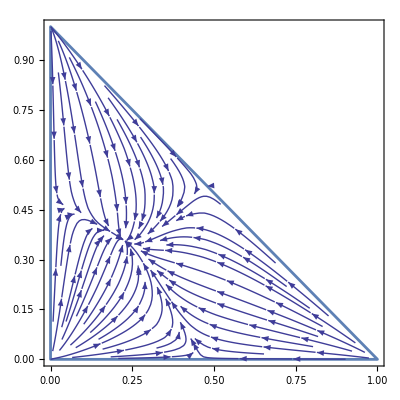

```mathematica
StreamPlot[{dy1[y1,y2]//N,dy2[y1,y2]//N},{y1,0,1},{y2,0,1},Frame->True,StreamStyle->Directive[Black,Thick],StreamPoints->Fine,StreamMarkers->{"PinDart"},StreamScale->{Large,None,None},RegionFunction->Function[{x,y,vx,vy,n},x+y<=1&&x>=0&&y>=0],RegionFillingStyle->None,StreamColorFunction->None]
```

### Type 2 Conformists

```mathematica
imglist={};
For[γ=0.3,γ<=0.9,γ=γ+0.3,
dy1[y1_,y2_]:=y1(typ2p[γ,{y1,y2},q1,1] q1-(typ2p[γ,{y1,y2},q1,1] q1 y1+typ2p[γ,{y1,y2},q2,2] q2 y2+typ2p[γ,{y1,y2},q3,3] q3 (1-y1-y2)));
dy2[y1_,y2_]:=y2 (typ2p[γ,{y1,y2},q2,2] q2-(typ2p[γ,{y1,y2},q1,1] q1 y1+typ2p[γ,{y1,y2},q2,2] q2 y2+typ2p[γ,{y1,y2},q3,3] q3 (1-y1-y2)));
y1=.;
y2=.;
sol=NSolve[{dy1[y1,y2]==0,dy2[y1,y2]==0},{y1,y2},Reals];
data={y1,y2}/.sol;
relData=Select[data,#⟦1⟧>0&&#⟦2⟧>0&&Total[#]<=1&&Total[#]≥0&];
p1=ListPlot[relData,PlotStyle->{Black,PointSize[0.025]}];
(*p2=ListPlot[relData,PlotStyle->{White,PointSize[0.015]}];*)
p3=ListPlot[{{{1,0}},{{0,1}},{{0,0}}},PlotStyle->{{Directive[cols⟦1⟧,PointSize[0.03]]},{Directive[cols⟦2⟧,PointSize[0.03]]},{Directive[cols⟦3⟧,PointSize[0.03]]}}];
p4=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{White,PointSize[0.015]}];
points=Show[(*p1,*)p3,p4];
(*cplt=ContourPlot[y1(typ2p[γ,{y1,y2},q1,1] q1-(typ2p[γ,{y1,y2},q1,1] q1 y1+typ2p[γ,{y1,y2},q2,2] q2 y2+typ2p[γ,{y1,y2},q3,3] q3 (1-y1-y2)))==0,{y1,0.0001,0.9999},{y2,0.0001,0.9999},RegionFunction->Function[{y1,y2},y1+y2≤1],PlotRange->All,ContourStyle->Darker[Red]];
cplt2=ContourPlot[y2 (typ2p[γ,{y1,y2},q2,2] q2-(typ2p[γ,{y1,y2},q1,1] q1 y1+typ2p[γ,{y1,y2},q2,2] q2 y2+typ2p[γ,{y1,y2},q3,3] q3 (1-y1-y2)))==0,{y1,0.0001,0.9999},{y2,0.0001,0.9999},RegionFunction->Function[{y1,y2},y1+y2≤1],PlotRange->All,ContourStyle->Darker[Blue]];*)
sp=StreamPlot[{dy1[y1,y2],dy2[y1,y2]},{y1,0.0001,0.999},{y2,0.0001,0.9991},Frame->True,StreamStyle->Black,StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,RegionFunction->Function[{x,y,vx,vy,n},x +y≤1&&x≥0&&y≥0],RegionFillingStyle->None];
psim=Show[tlp,
Graphics[GeometricTransformation[First[Show[sp]],trans]],
(*Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],*)
Graphics[GeometricTransformation[First[Show[points]],trans]],
(*Graphics[Text["Copying intensity\n γ = "<>ToString[γ],{0.1,0.7}]],*)
Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]]
];(*,
Graphics[GeometricTransformation[First[parpl],trans]]*)
AppendTo[imglist,{γ,psim}]
]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

```mathematica
imglist
```

{{0.3,-Graphics-},{0.6,-Graphics-},{0.9,-Graphics-}}

## Connecting to data

```mathematica
diamond=.;
```

```mathematica
diamond=Graphics[{Black,Rotate[Rectangle[],45Degree]}];
```

```mathematica
Lighter[cols,0.7]
```

{RGBColor[0.9642166, 0.8833122999999999, 0.7426153],RGBColor[0.8105251, 0.8520337, 0.9129394],RGBColor[0.8680543, 0.9074707, 0.7584655]}

### Type 1 Conformists

```mathematica
dataplotstype1conformists=Table[Show[Graphics[{EdgeForm[{Black,Thin}],Table[{Blend[Lighter[cols,0.5],{rawtype1conf⟦j,2;;⟧⟦i⟧⟦4⟧,1-rawtype1conf⟦j,2;;⟧⟦i⟧⟦3⟧-rawtype1conf⟦j,2;;⟧⟦i⟧⟦4⟧,rawtype1conf⟦j,2;;⟧⟦i⟧⟦3⟧}],RegularPolygon[trans[{rawtype1conf⟦j,2;;⟧⟦i⟧⟦2⟧,1-rawtype1conf⟦j,2;;⟧⟦i⟧⟦2⟧-rawtype1conf⟦j,2;;⟧⟦i⟧⟦1⟧}],{0.01,11},6]},{i,1,Length[rawtype1conf⟦j,2;;⟧]}]},Frame->False,PlotRange->{{-0.05,1.05},{-0.05,(√3)/2+0.05}}],ListPlot[{internal⟦All,2⟧⟦j⟧},Joined->True,Axes->False,PlotMarkers->{diamond,Scaled[0.05]},PlotStyle->Opacity[0.5]],tlp],{j,1,Length[filecounter],1}];
```

```mathematica
(*dataplots=Table[Show[triangle,ListPlot[datatransformedlist⟦i⟧,InterpolationOrder->2,PlotStyle->PointSize[Medium],Axes->False,AspectRatio->1],ListPlot[{internal⟦All,2⟧⟦i⟧},Joined->True,Axes->False,PlotMarkers->{◆,Scaled[0.05]}]],{i,1,Length[filenames],1}];*)
```

```mathematica
imagestoplot={Show[dataplotstype1conformists⟦7⟧,imglist⟦All,2⟧⟦1⟧,PlotRange->All],Show[dataplotstype1conformists⟦13⟧,imglist⟦All,2⟧⟦2⟧,PlotRange->All],Show[dataplotstype1conformists⟦19⟧,imglist⟦All,2⟧⟦3⟧,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
imagestoplot⟦3⟧
```

-Graphics-

### Type 2 Conformists

```mathematica
dataplotstype2conformists=Table[Show[Graphics[{EdgeForm[{Black,Thin}],Table[{Blend[Lighter[cols,0.5],{rawtype2conf⟦j,2;;⟧⟦i⟧⟦4⟧,1-rawtype2conf⟦j,2;;⟧⟦i⟧⟦3⟧-rawtype2conf⟦j,2;;⟧⟦i⟧⟦4⟧,rawtype2conf⟦j,2;;⟧⟦i⟧⟦3⟧}],RegularPolygon[trans[{rawtype2conf⟦j,2;;⟧⟦i⟧⟦2⟧,1-rawtype2conf⟦j,2;;⟧⟦i⟧⟦2⟧-rawtype2conf⟦j,2;;⟧⟦i⟧⟦1⟧}],{0.01,11},6]},{i,1,Length[rawtype2conf⟦j,2;;⟧]}]},Frame->False,PlotRange->{{-0.05,1.05},{-0.05,(√3)/2+0.05}}],ListPlot[{internal⟦All,2⟧⟦j⟧},Joined->True,Axes->False,PlotMarkers->{diamond,Scaled[0.05]},PlotStyle->Opacity[0.5]],tlp,Graphics[Text[Style["Morph 1",FontFamily->"Calibri",12,cols⟦1⟧],{1.2,0}]],
Graphics[Text[Style["Morph 2",FontFamily->"Calibri",12,cols⟦2⟧],{-0.2,0}]],
Graphics[Text[Style["Morph 3",FontFamily->"Calibri",12,cols⟦3⟧],{0.6-0.09,(√3)/2+0.12}]],PlotRange->All],{j,1,Length[filecounter],1}];
```

```mathematica
{dataplotstype2conformists⟦7⟧,dataplotstype2conformists⟦13⟧,dataplotstype2conformists⟦19⟧}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
type2imgstopl={Show[dataplotstype2conformists⟦7⟧,imglist⟦All,2⟧⟦1⟧,PlotRange->All],Show[dataplotstype2conformists⟦13⟧,imglist⟦All,2⟧⟦2⟧,PlotRange->All],Show[dataplotstype2conformists⟦19⟧,imglist⟦All,2⟧⟦3⟧,PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
type2imgstopl⟦1⟧
```

-Graphics-